# MATH7501 Practical 11 (Week 12), Semester 1-2021

## Topic: Probability Distributions

Author:  Aminath Shausan
Date: 21-05-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with units 9 and 10 contents  of the reading materials for MATH7501

# Resources

Chapters 9 and 10: Computation of mean, variance, expectation, gradient decent method

https://en.wikipedia.org/wiki/Rayleigh_distribution

# Section 1: The Rayleigh Distribution

In probability theory and statistics,the Rayleigh distribution is a continuous probability distribution for nonnegative-valued random variables.

The notation X~Rayleigh(σ) means that the random variable X has a Rayleigh distribution with shape parameter σ.The probability density function  (pdf) is:

```mathematica
Subscript[f, X](x)= {{{x/σ^2 e^(-x^2/(2 σ^2))  ,    x ≥0, σ>0}, {0,                              x <0}}
```

```mathematica
Q1) Plot the pdf of X for σ = 0.5, 1, 2, 3
```

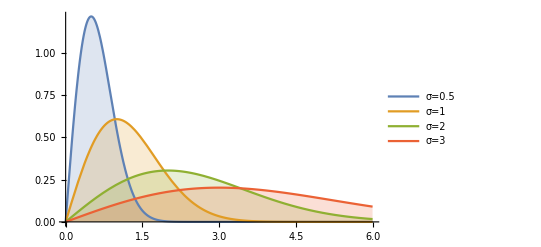

```mathematica
Plot[Table[PDF[RayleighDistribution[σ],x],{σ,{.5,1,2,3}}]//Evaluate,
{x,0,6},Filling->Axis,PlotRange->All, PlotLegends->{"σ=0.5", "σ=1", "σ=2", "σ=3"}]
```

```mathematica
Q2) Show that the cumulative distribution function (cdf) of X is 
                   Subscript[F, X](x)= {{{1-e^(-x^2/(2 σ^2))  , x ≥0}, {0,             x <0}}
```

```mathematica
Subscript[F, X](x) = P(X≤x)
```

```mathematica
f[x_]:=x/σ^2 E^(-x^2/(2 σ^2))(*Rayleigh probability density function*)
```

```mathematica
Integrate[f[x],{x,0,u}] (*CDF*)
```

1-ⅇ^(-u^2/(2 σ^2))

```mathematica
Q3) Show that Subscript[f, X](x) is a valid probability density function by showing that the integral over [0, ∞) is 1
```

```mathematica
Integrate[f[x],{x,0,∞}, Assumptions -> σ>0]
```

1

```mathematica
(*using numerical approximation to compute the mean when σ =1*)
NIntegrate[x E^(-x^2/2), {x,0,∞}]
```

1.

```mathematica
Q4) Show that  the mean of X ~ Rayleigh(σ) = σ√π/2
```

```mathematica
Subscript[μ, X] = E(X)  = ∫_0^∞ Subscript[xf, X](x)dx
                         = ∫_0^∞ x x/σ^2 e^(-x^2/(2 σ^2))dx
```

```mathematica
Integrate[x f[x],{x,0,∞}, Assumptions -> σ>0]  (*mean (μ) *)
```

√(π/2) σ

```mathematica
(*using numerical approximation to compute the mean when σ =1*)
```

```mathematica
NIntegrate[x  x E^(-x^2/2),{x,0,∞}]
```

1.25331

```mathematica
δ = 0.01
```

0.01

```mathematica
Total[Table[x  x E^(-x^2/2)δ,{x,0,10,δ}]]
```

1.25331

```mathematica
Q5)Show that the variance of X~ Rayleigh(σ) = σ^2((4-π)/2)
Subscript[σ^2, X]=var(X) = E[X^2]-Subscript[μ, X]^2
E[X^2] = ∫_(-∞)^∞ x^2 Subscript[f, X](x)dx
              = ∫_0^∞ x^2 x/σ^2 e^(-x^2/(2 σ^2))dx
```

```mathematica
Integrate[x^2 f[x],{x,0,∞}, Assumptions -> σ>0] (*compute second moment (E[X^2]*)
```

2 σ^2

```mathematica
(*using numerical approximation to compute the second moment when σ =1*)
```

```mathematica
NIntegrate[x^2 x E^(-x^2/2),{x,0,∞}]
```

2.

```mathematica
Total[Table[x^2 x E^(-x^2/2)δ,{x,0,10,δ}]]
```

2.

```mathematica
(*variance*)
E[X^2]- μ^2 = 2 σ^2 -(√(π/2) σ)^2
```

2 σ^2-(π σ^2)/2

# Section 2: Simple Linear Regression Problem

Consider the simple linear regression problem  with data points  (x_1,y_1), ..., (x_n, y_n). The aim is to seek β_0 and β_1 to fit the line,
                                                    y = β_0 + β_1x,
 by minimizing the loss function
                                                L(β_0 β_1) = ∑_(i=1)^n (y_i-(β_0+β_1 x_i))^2 .
  Here, β_0 and β_1 are the slope and the intercept, respectively, of the line of best fit.

Q6) Compute an expression for the gradient of L(β_0 β_1)